```mathematica
f=Function[x,Sin[x]];
g1=Function[x,Exp[x]];
f[g1[x]]==0
```

Sin[ⅇ^x]==0

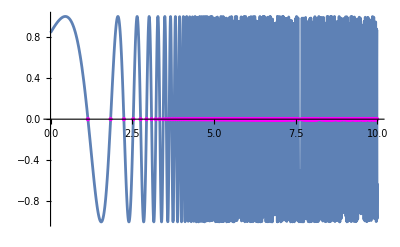

```mathematica
Plot[f[g1[x]],
{x,0,10},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]]
```

In order to solve for these solutions, one would first solve f(u) = k to find the values that need to be plugged into f. Then set g(x) = u for all u to find the values x that would satisfy both equations.

The density of solutions increases exponentially as x increases. The density of solutions of f is based on the value inputted. The faster the x is growing in Sin[x], the greater the density of solutions. And since g gets really big really fast as x increases that means the density of f will increase really fast as x increases.  However it is impossible to graph all the solutions as there are infinite solutions to f = 0.  It is also impossible to solve for all solutions because e is not linear or periodic.

```mathematica
g2=Function[{a,x},a*Cos[x]];
f[g2[a,x]]==0
```

Sin[a Cos[x]]==0

```mathematica
Manipulate[
Plot[f[g2[a,x]],
{x,0,10},(* change domain as desired *)
MeshFunctions->{Function[{x,y},y]},
Mesh->{{0}},(* Note: k goes in the list *)
MeshStyle->Directive[PointSize@Medium,Magenta]],
{{a,1}, (* initial value for a *)
Pi,10*Pi} (* range for a *)
]
```

The density of solutions increases as a increases when x is around a multiple of pi/2. This is because the amplitude of the cos curve increases as a increases. Thus the rate of change of g increases as a increases.  Since the solutions for f(u) = k doesn’t change, only g will affect the solutions and the density of these solutions. Lastly, there are also infinitely many solutions so its impossible to graph all of them. However, I do believe it is possible to solve for all the solutions for a given a because both f and g are periodic functions.